# Generate Plots

To the point, just the facts, ma’am, leave all the trial and error to the main, long notebook GWExopEcc2.nb.

## Strain calculations for exoplanets in the Caltech database. Calculate with eccentricity and distance, etc, the strain at Earth. Frequencies relevant for LISA.

## Notes

20171013 Started taking best bits from GWExopEcc2.nb, and trying to generate the publication quality plots here and not in XMGrace with *.dat files.
20180118 Found that I had to take the dbase “by hand” the URLExecute command in ExoDBase.np tosses errors.

## References

P. Amaro-Seoane et al. “Triplets of supermassive black holes: astrophysics, gravitational waves and detection,” MNRAS 402 2308-2320 (2010);
P. C. Peters and J. Mathews, “Gravitational Radiation from Point Masses in a Keplerian Orbit,” Phys. Rev. 131 (1963) 435-440.
Michele Maggiore, “Gravitational Waves. Volume 1: Theory and Experiments,” Oxford Univ. Press, 2008.

## Directories

```mathematica
(*myDir = "/scratch/gabella/Documents/astro/exop/";*)
(*thisDir = "/home/gabella/Documents/astro/exop/exoplanetsMath/";*)
thisDir = NotebookDirectory[];
csvDir = thisDir <>"dbases/";
pixDir = thisDir <>"pix/";
```

## Read the CSV file, filter data for non-null entries.

### Run ExoDBase.nb to re-create the cvs file.

```mathematica
csvFileName = csvDir<>"exopP_20180325_114502.csv"
```

/home/gabella/Documents/astro/exop/exoplanetsMath/dbases/exopP_20180325_114502.csv

Find the date-time stamp...lots of StringSplit[]’s.  Will be used in output file names.

```mathematica
dateTimeStamp = Block[{aa,bb,cc},
aa = StringSplit[csvFileName,"/"][[-1]];  (* Filename with stamp is last element. *)
bb = StringSplit[aa,"."][[1]]; (* Drop the .csv extension . *)
cc = StringSplit[bb, "_"]; (* Last two elements are the YYYYMMDD and the HHMMSS strings. *) 
cc[[2]]<>"_"<>cc[[3]]
]
```

20180325_114502

The first row has the columns and other info.  Mathematica lets the data be mixed format, some are strings others reals.

```mathematica
alldata = Import[csvFileName, "Data"];
```

```mathematica
alldata[[1;;3]] //TableForm(* Look for the row headers. *)
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92

Test which row has the headers in it, starting at row 1.  Return -999 if there is no element “pl_hostname” at the [[n,1]] position.

```mathematica
irow = 1; 
trowHeaders = -999;
For[irow=1, irow≤Length[alldata], irow+=1,
If[ StringMatchQ[ alldata[[irow,1]], "pl_hostname" ], trowHeaders=irow; Break[]  ]
](* end For *)
trowHeaders
```

1

```mathematica
rowHeaders=trowHeaders; rowDataStart=rowHeaders+1;  (* row with the headers, etc . *)
```

```mathematica
Print[ alldata[[rowHeaders]]  ]
```

{pl_hostname,pl_letter,pl_discmethod,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx}

Cols are 
pl_hostname, pl_letter, pl_orbper, pl_orbsmax, pl_orbeccen, pl_bmassj, st_dist, st_mass, pl_name, pl_massj   (??not same as above)
# COLUMN pl_hostname:    Host Name
# COLUMN pl_letter:      Planet Letter
# COLUMN pl_orbper:      Orbital Period [days]
# COLUMN pl_orbsmax:     Orbit Semi-Major Axis [AU]
# COLUMN pl_orbeccen:    Eccentricity
# COLUMN pl_bmassj:      Planet Mass or M*sin(i)[Jupiter mass]
# COLUMN st_dist:        Distance [pc]
# COLUMN st_mass:        Stellar Mass [Solar mass]
# COLUMN pl_name:        Planet Name
# COLUMN pl_massj:       Planet Mass [Jupiter mass]
# COLUMN st_plx:	Star parallax distance [mas], NB: dist in pc is 1000.0/st_plx (in mas)

Find the type of the data fields, when they are actually numbers and not blanks!  Mix of Strings and Reals.

```mathematica
Print["Length of the column, the number of columns is ", Length[ alldata[[rowDataStart]] ]  ]
```

Length of the column, the number of columns is 11

Make a dictionary, aka Association in Mathematica, with the header strings to the column numbers / array indices.

```mathematica
cols = <||>;  (* Use an Association as an enum, or Dictionary *)
For[icnt=1, icnt≤Length[ alldata[[rowHeaders]] ], icnt+=1,
AppendTo[cols,alldata[[rowHeaders,icnt]]->icnt]
];
```

```mathematica
Keys[cols]
```

{pl_hostname,pl_letter,pl_discmethod,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx}

```mathematica
{cols["pl_hostname"], cols["pl_orbper"]}
```

{1,4}

#### Filter data for the non-null data only.

Some of the fields are blank, so drop those planets from consideration.  Define a filter function.

```mathematica
Clear[filterBlanks2]
filterBlanks2[aa_, filterInd_]:=Module[{retList, blankList},
retList={};
blankList={};
For[i=1,i<=Length[aa], i++,
If[ NumberQ[ aa[[i,filterInd]] ], AppendTo[retList, aa[[i]] ], AppendTo[blankList, aa[[i]] ]]
];
{retList, blankList}
]
```

Filter the blanks in all masses, eccentricity, semimajor axis, and distance.  Below one at a time.

```mathematica
Print["Length alldata ",Length[alldata] ]
tempdata = alldata;
tempdata= filterBlanks2[tempdata[[rowDataStart;;]], cols["pl_orbeccen"] ][[1]]; Print[ "Number with pl_orbeccen ", Length[tempdata]]
tempdata= filterBlanks2[tempdata, cols["pl_orbper"] ][[1]]; Print[ "Number with pl_orbper ",Length[tempdata] ]
tempdata = filterBlanks2[tempdata, cols["pl_orbsmax"] ][[1]]; Print["Number with pl_orbsmax ",Length[tempdata] ]
tempdata = filterBlanks2[tempdata, cols["pl_bmassj"] ][[1]]; Print["Number with pl_bmassj ",Length[tempdata] ] (* use pl_bmassj not pl_massj *)
tempdata = filterBlanks2[tempdata, cols["st_dist"] ][[1]]; Print["Number with st_dist ",Length[tempdata] ]
tempdata = filterBlanks2[tempdata, cols["st_mass"] ][[1]]; Print["Number with st_mass ",Length[tempdata] ]
```

Length alldata 3707

Number with pl_orbeccen 1170

Number with pl_orbper 1170

Number with pl_orbsmax 1105

Number with pl_bmassj 1024

Number with st_dist 918

Number with st_mass 908

The filtered data, and it should have same length as last step above.

```mathematica
fdata = tempdata; (* The filtered data. *)
Length[fdata]
```

908

## Eccentric orbits from the exoplanet database.

### Some constants. Work in SI units. Okay, join the astro / GR world and look at units of length for mass, etc, that is G=c=1 type of unit conversion.

```mathematica
massSun = 1.989 10^30; (*kg *)
massJ = 1.898 10^27; (* kg *)
massE = 5.972 10^24; (* kg *)
massJe = massJ/massE; (* Jupiter mass is 317.9 earth masses *)
massJs = massJ/massSun; (* relative to the sun's mass *)
pc = 30.86 10^15; (* meters, parsec *)
au = 149.6 10^9; (* meters, astron unit *)
cee = 299792458.0; (* meters/s, speed of light *)
secsYear = 365.24*24.0*3600.0; (* s, number of seconds in a year *)
secsDay = 24.0*3600.0; (* s, number of seconds in a day *)
bigG = 6.67408 10^-11; (* SI Gravitational constant, m^3/kg/s *)

rscon = 2*bigG*massSun/cee^2 (* 2955.43 m, solar mass Scharzschild radius *)
lunits =bigG*massSun/cee^2 (* meters per solar mass, units of G=c=1, no factor of 2 as in Schwarzschild radius *)
masscon = lunits; (* m, G Msol/c^2, for 1 solar mass *)

powercon = cee^5/bigG  (* 3.628 10^52 W, c^5/G, W/unit since P is dimensionless in G=c=1 units *)
energycon = cee^4/bigG  (* 1.210 10^44 J/m, c^4/G *)
```

2954.03

1477.01

3.62837×10^52

1.2103×10^44

```mathematica
secsYear
```

3.15567×10^7

### The functions of interest.

Moved the g(n,e)  here ggXX[] comparison section to file ThreeGsGWEccen.nb .  All the forms, including out shortened form, all agree.

Amaro-Seoane et al. hence the last letters “AS” for the “big A” function in their paper.

```mathematica
Clear[bigAAS, bigBAS, jj]
jj = BesselJ;
bigAAS[n_,e_]:=jj[n-2,n e]-2 jj[n, n e]+jj[n+2,n e]
bigBAS[n_,e_]:=jj[n-2,n e]-2 e jj[n-1,n e]+2/n jj[n,n e]+2 e jj[n+1,n e]-jj[n+2,n e]
ggAS[n_, e_]:=n^4/32(bigBAS[n,e]^2 + (1-e^2)bigAAS[n,e]^2+4/(3 n^2)jj[n,n e]^2)
```

Amaro-Seoane et al., h_n Eqn. (9).  These also show up in Maggiore’s book, section on the Kepler orbits for finding the GW power and spectrum.

```mathematica
Clear[chirpM,redM, totM, fr, hh]
chirpM[m1_,m2_]:=(m1 m2)^(3/5)/(m1+m2)^(1/5)
redM[m1_,m2_]:=(m1 m2)/(m1+m2)
totM[m1_,m2_]:=m1+m2
fr[m1_,m2_,a_]:=1/(2 π)√((bigG(m1+m2))/a^3)
hh [n_,e_,m1_,m2_,a_, dL_]:= bigG^(5/3)/cee^4 2 √(32/5)chirpM[m1,m2]^(5/3)/(n dL)(2π fr[m1,m2,a])^(2/3) √ggAS[n,e]  (* Subscript[d, L] is luminosity distance d=Subscript[d, L]/(1+z), z=0 for us, Subscript[f, r] is orbital freq *)
```

```mathematica
Table[{nn, ggAS[nn,0.95]}, {nn, 1, 200, 20}]//TableForm
```

1 | 0.0369921
21 | 1.34861
41 | 10.1728
61 | 25.5646
81 | 42.1575
101 | 55.7299
121 | 64.2902
141 | 67.6221
161 | 66.5335
181 | 62.2382

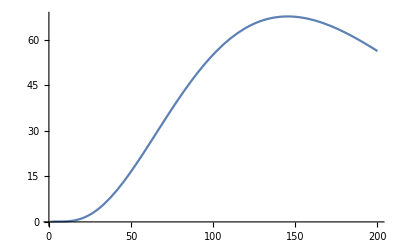

```mathematica
Plot[ggAS[nn,0.95], {nn, 1, 200}]
```

The numerical fit from GWExopEcc2.nb .

```mathematica
Clear[fitEcc2N2]
fitEcc2N2=FittedModel[ⅇ^(9.521217921844688 x) (0.5899926687166828-1.4130060483325517 x+0.8921018741263468 x^2)]
```

FittedModel[ⅇ^(9.52122 x) (0.589993-1.41301 x+0.892102 x^2)]

```mathematica
fitEcc2N2[0.7] (* For e=0.7 29.8196 *)
```

29.8196

Find the mode number n_max where g(n,e) falls to 0.05.  Also n_min, usually either 1 or 2.

```mathematica
Clear[aNmax];
aNmax[ecc_]:=If[ecc==0, 2, Max[ {3, Floor[fitEcc2N2[ecc]+1] } ]  ] (* Changed 20180119, want modes {1,2,3} for all small but non-zero eccentricities. *)
Clear[aNmin];
aNmin[ecc_]:=If[ecc==0,2, 1](* A little silly, but played with n=2 for e=0 since the only one but want a range, so 1 to 2 for e=0. *)
```

#### Amaro-Seoane et al. enhancement DO NOT DO THIS!

Now for the hf calculation following Amaro-Seoane et al.  Already have h with correct units (unitless) above.  Note the G^(5/3)/c^4~6.3×10^-55.  But for strain sensitivity (??), do the AS eqn. (10) enhancement,
 hobs,n = h_n  √(T f_(r n))   , where T is max(T_orb, T_obs), 
 so that T f_(f n)= 1 or N_orbs, the latter if observed for many orbital periods.  So their formula is like a sqrt(N) incoherent addition for the noise and for thre signal it should add like N.  A lot like pulsar analysis.
Used 3 years and 10 years for LISA observing T_obs...in previous exoplanet work (Hot Jupiters).  I think almost all T_orb are less than that.

```mathematica
rootNfcn := Sqrt[ Max[ #1, #2]*#3/#1 ]&; (* #1 is Subscript[t, orb], #2 is Subscript[t, obs], same units!, #3 is the n of the GW harmonic *)
```

## The strain versus frequency of the n-th GW mode.

Leave out a lot of the “cleverness” in the handling of the column names, etc.  “Just the facts, ma’am.”

```mathematica
Length[fdata]
```

908

For each row in the data list, calculate the mode frequencies, and use the listed parameters to come up with the dimensionless strength h(n), for each mode.  imode Amaro-Seoane adjustment yet.

```mathematica
{alldata[[1]]}~Join~fdata[[1;;2]]//TableForm
```

pl_hostname | pl_letter | pl_discmethod | pl_orbper | pl_orbsmax | pl_orbeccen | pl_bmassj | st_dist | st_mass | rowupdate | st_plx
HD 142022 A | b | Radial Velocity | 1928. | 3.03 | 0.53 | 5.1 | 35.87 | 0.99 | 2014-05-14 | 27.88
HD 39091 | b | Radial Velocity | 2151. | 3.38 | 0.6405 | 10.27 | 18.21 | 1.1 | 2014-07-23 | 54.92

Use the association/dictionary cols to get the right columns using the above text.  Practice with this association/dictionary a bit, check it.

```mathematica
{cols["pl_orbper"],cols["pl_bmassj"], cols["st_dist"]}
```

{4,7,8}

```mathematica
{Length[fdata], Length[fdata[[1]] ]}
```

{908,11}

```mathematica
fdata[[1]]
```

{HD 142022 A,b,Radial Velocity,1928.,3.03,0.53,5.1,35.87,0.99,2014-05-14,27.88}

```mathematica
fdata[[1]][[cols["pl_orbeccen"] ]]
```

0.53

All calculations in SI units, see constants above.

```mathematica
hhVfreq={}; (* Hold data for plotting, giant flat list. *)

For[ipl=1, ipl≤Length[fdata], ipl++,
{Block[{row, m1,m2, smax, dL},  (* use the Block[] to have some local variables. *)
frow = fdata[[ipl]];  (* Whole row. *)
orbeccen = frow[[cols["pl_orbeccen"] ]];  (* Pick out the eccentricity. *)
(*modeMax = Ceiling[ fitEcc2N2[orbeccen] ];(* max harmonic n for eccen *)*)
modeMax = aNmax[ orbeccen ];
modeMin = aNmin[ orbeccen ];
If[ipl<2,Print["orbeccen ", orbeccen,  " modeMin ", modeMin," modeMax ", modeMax]]; (* Check the ipl=1 row with above lookup. *)
m1 = frow[[cols["pl_bmassj"]] ]*massJ;
m2= frow[[cols["st_mass"]] ]*massSun;
smax = frow[[cols["pl_orbsmax"]] ]*au ;
dL = frow[[cols["st_dist"]]  ]*pc;
(*freq0= fr[ m1, m2, smax ];*)
freq0= 1.0/( frow[[cols["pl_orbper"] ]]*secsDay );
frontCoeff = bigG^(5/3)/cee^4 2 √(32/5)chirpM[m1,m2]^(5/3)/dL(2π freq0)^(2/3);(* see above, missing the sqrt(g(n,e))/n in Amaro-Seoane's eqn. *)
],(* end Block *)
  
For[imode = modeMin, imode ≤  modeMax, imode++,
Block[{gwfreq, hh},
gwfreq = freq0*imode;
hh = frontCoeff*Sqrt[ggAS[imode, orbeccen] ]/imode;
hhVfreq~AppendTo~{gwfreq, hh};
](* end second Block *)
](* end second For loop *)
}(* end {} for first For loop *)
](* end first For *)
```

orbeccen 0.53 modeMin 1 modeMax 15

```mathematica
{Length[hhVfreq], Length[hhVfreq[[3]] ]}
hhVfreq[[1;;5]]
```

{6316,2}

{{6.00315×10^-9,1.87028×10^-26},{1.20063×10^-8,2.17407×10^-26},{1.80095×10^-8,2.88216×10^-26},{2.40126×10^-8,2.66486×10^-26},{3.00158×10^-8,2.1936×10^-26}}

Quick plot of list, freq (Hz)  and hh (dimensionless).  You can see the modes trace out the shape of g(n,e) for a given eccentric system.

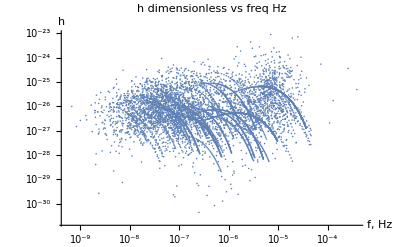

```mathematica
ListLogLogPlot[hhVfreq,
PlotLabel->"h dimensionless vs freq Hz",
AxesLabel->{"f, Hz", "h"}]
```

Now do the same with the Amaro-Seoane et al. factor of sqrt(N_obs) to calculate their h_obs, still dimensionless.  DO NOT DO THIS!!  So same as above.

```mathematica
hhVfreqObs={}; (* Hold data for plotting, giant flat list. *)
tobs = 1.*secsYear;  (* Match the Larson curve generator, default is ROOT SPECTRAL DENSITY but this is one year integration for dimensionless strain. *)

For[ipl=1, ipl≤Length[fdata], ipl++,
{Block[{row, m1,m2, smax, dL},  (* use the Block[] to have some local variables. *)
frow = fdata[[ipl]];
orbeccen = frow[[cols["pl_orbeccen"] ]];
(*modeMax = Ceiling[ fitEcc2N2[orbeccen] ];(* max harmonic n for eccen *)*)
modeMax = aNmax[ orbeccen ];
modeMin = aNmin[ orbeccen ];
If[ipl<2,Print["orbeccen ", orbeccen,  " modeMin ", modeMin," modeMax ", modeMax]]; (* check the above lookup *)
m1 = frow[[cols["pl_bmassj"]] ]*massJ;
m2= frow[[cols["st_mass"]] ]*massSun;
smax = frow[[cols["pl_orbsmax"]] ]*au ;
dL = frow[[cols["st_dist"] ]]*pc;
freq0= 1.0/( frow[[cols["pl_orbper"] ]]*secsDay );
frontCoeff = bigG^(5/3)/cee^4 2 √(32/5)chirpM[m1,m2]^(5/3)/dL(2π freq0)^(2/3);

(* see above, missing the sqrt(g(n,e))/n in Amaro-Seoane's eqn. *)
],(* end Block *)  

For[imode = modeMin, imode ≤  modeMax, imode++,
Block[{gwfreq, hh, factAS},
gwfreq = freq0*imode;
factAS = rootNfcn[  1/freq0, tobs, imode]; (* Torb, Tobs, n-mode *)
factAS = 1.0;  (* Do not do this AS factor, just instaneous values and average the noise sensitivity of LISA! *)
hh = frontCoeff*Sqrt[ggAS[imode, orbeccen] ]/imode *factAS;
hhVfreqObs~AppendTo~{gwfreq, hh};
](* end second Block *)
](* end second For loop *)
}(* end {} for first For loop *)
](* end first For *)
```

orbeccen 0.53 modeMin 1 modeMax 15

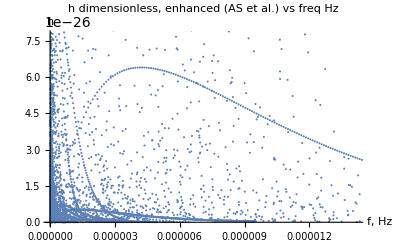

```mathematica
ListPlot[hhVfreqObs,
PlotLabel->"h dimensionless, enhanced (AS et al.) vs freq Hz",
AxesLabel->{"f, Hz", "h"}]
```

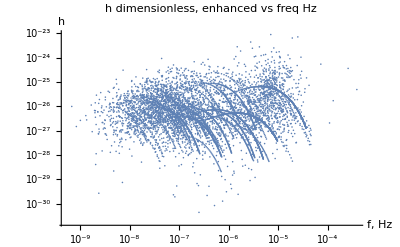

```mathematica
ListLogLogPlot[hhVfreqObs,
PlotLabel->"h dimensionless, enhanced vs freq Hz",
AxesLabel->{"f, Hz", "h"}]
```

### The Larson curve from http://www.srl.caltech.edu/~shane/sensitivity/MakeCurve.html , for dimensionless strain says 1 year integration time (?)

```mathematica
fname = "scg_5672_hdimless_1yearInten.dat";
dataLarson = Import[fname];
```

```mathematica
dataLarson[[1;;20]]
```

{{#,Code:,cgiSensePlot.c,v4.0,(sll,-,13,February,2009,Build)},{#,from,WWW,Sensitivity,Curve,Generator,located,at:},{#,http://www.srl.caltech.edu/~shane/sensitivity/MakeCurve.html},{#,EQUAL,ARM,Space,Based,Observatory,Sensitivity,Curve},{#,Polarization,and,All,Sky,Averaged},{#},{#,For,this,data,file:},{#,SNR,=,1.},{#,Armlength,=,5.×10^9,meters},{#,Optics,diameter,=,0.3,meters},{#,Wavelength,=,1064.,nanometers},{#,Laser,power,=,1.,Watts},{#,Optical,train,efficiency,=,0.3},{#,Accleration,noise,=,3.×10^-15,m/(s^2,root,Hz)},{#,Position,noise,=,2.×10^-11,m/(root,Hz)},{#,Sensitivity,Floor,Set,by,Position,Noise,Budget},{#,Output,Curve,type,is,Dimensionless,strain,(1,yr,integration)},{#,Astrophysical,Noise,is,No,White,Dwarf,Noise},{#},{#}}

```mathematica
dataOnly = dataLarson[[23;;]];
```

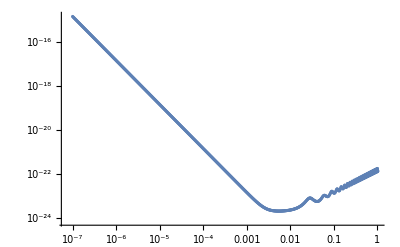

```mathematica
ListLogLogPlot[dataOnly]
```

Put them on the same plot.

```mathematica
{Length[hhVfreq], Length[dataOnly]}
```

{6316,900}

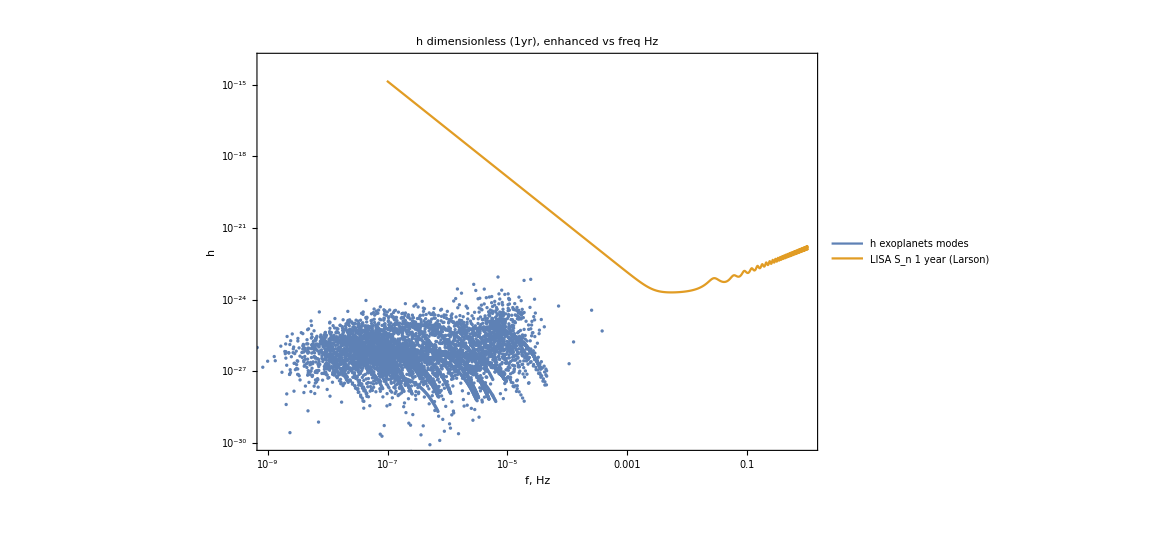

```mathematica
plot1year = ListLogLogPlot[{hhVfreq,dataOnly},
PlotRange->{{10^-9, 10^0},{10^-30,10^-14}},
Joined->{False, True},
PlotLabel->"h dimensionless (1yr), enhanced vs freq Hz",
AxesLabel->{"f, Hz", "h"},
PlotLegends->Placed[LineLegend[{"h exoplanets modes", "LISA S_n 1 year (Larson)"}, Joined->True],{Right, Top}],
PlotTheme->"Detailed",
ImageSize->{12.0, 8.0}*72.0]
```

```mathematica
Export["OneYearLarson.png", plot1year,ImageSize->{12.0, 8.0}*72.0]
```

OneYearLarson.png

So the question to answer AGAIN is does longer time lower the LISA dimensionless h_sensitivity and raise the data h_obs??  NO!
If you are looking at a source, you can lower the LISA strain or strain sensitivity by sqrt (Time) essentially or sqrt(N observations) but not also raise your data.
See Bill’s work on the sum over the GW modes for determining a single (eccentric) planets SNR wrt the Sn(f) for LISA.  Reduction shows up there, I think.  (weg)

```mathematica
(* Fix for a ten year average of the Larson h plot. *)
{AvgYears, StrAvgYears, StrAvgYears2}={10.0, "10", "Ten"};  (* Make it easier to keep track in the plots below. *)
{AvgYears, StrAvgYears, StrAvgYears2}={4.0, "4", "Four"}; (* Cornish seems to think 4 years is better, the current mission plan? *)
{xx,yy} = Transpose[dataOnly];
dataOnlyNNyr = Transpose[{xx,yy/√AvgYears}];
{dataOnly[[1]], dataOnlyNNyr[[1]]}
```

{{9.76504×10^-8,1.46515×10^-15},{9.76504×10^-8,7.32573×10^-16}}

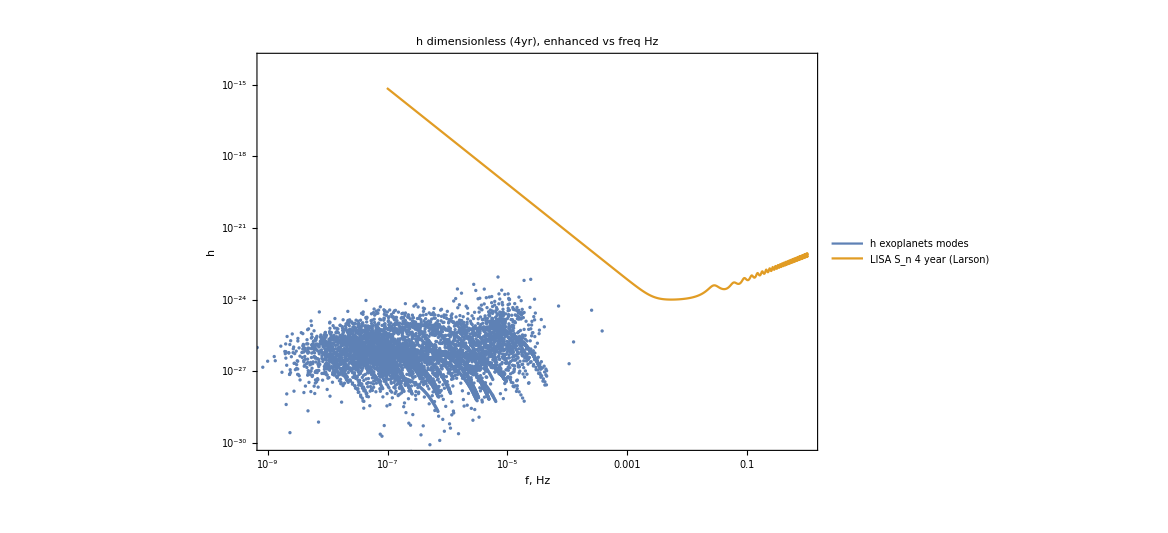

```mathematica
plotNNyear = ListLogLogPlot[{hhVfreq,dataOnlyNNyr},
PlotRange->{{10^-9, 10^0},{10^-30,10^-14}},
Joined->{False, True},
PlotLabel->"h dimensionless ("<>StrAvgYears<>"yr), enhanced vs freq Hz",
AxesLabel->{"f, Hz", "h"},
PlotLegends->Placed[LineLegend[{"h exoplanets modes", "LISA S_n "<>StrAvgYears<>" year (Larson)"}, Joined->True],{Right, Top}],
PlotTheme->"Detailed",
ImageSize->{12.0, 8.0}*72.0]
```

```mathematica
Export[StrAvgYears2<>"YearLarson.png", plotNNyear,ImageSize->{12.0, 8.0}*72.0]
```

FourYearLarson.png

## Diamond Planet, aka PSR J1719-1438 b

```mathematica
Keys[cols]
```

{pl_hostname,pl_letter,pl_discmethod,pl_orbper,pl_orbsmax,pl_orbeccen,pl_bmassj,st_dist,st_mass,rowupdate,st_plx}

Look for the Pulsar host star and then planet b in the filtered data fdata.

```mathematica
myHostStar = "PSR J1719-1438";
(*myHostStar = "PSR";*)
myPlanet = "b";
myRowStar={};
(*myRowPlanet = [];*)
For[irow=1, irow≤Length[fdata], irow+=1,
If[ StringMatchQ[ fdata[[irow,cols["pl_hostname"] ]],myHostStar] , myRowStar~AppendTo~irow  ]
] (* end For *)
myRowStar
```

{331}

```mathematica
fdata[[ myRowStar[[1]]]  ]
```

{PSR J1719-1438,b,Pulsar Timing,0.0907063,0.0044,0.06,1.2,1200.,1.4,2014-05-14,}

```mathematica
Ceiling[ fitEcc2N2[0.2] ]
```

3

## Repeat the previous strain calculations and frequency modes but for a single planet, or few planets.

```mathematica
plhhVfreq={}; (* Hold data for plotting, giant flat list. *)

For[ii=1, ii≤Length[myRowStar], ii++,
ipl=myRowStar[[ii]];
{Block[{row, m1,m2, smax, dL},  (* use the Block[] to have some local variables. *)
frow = fdata[[ipl]];  (* Whole row. *)
orbeccen = frow[[cols["pl_orbeccen"] ]];  (* Pick out the eccentricity. *)
(*modeMax = Ceiling[ fitEcc2N2[orbeccen] ];(* max harmonic n for eccen *)*)
modeMax = aNmax[ orbeccen ];
modeMin = aNmin[ orbeccen ];
If[ipl<2,Print["orbeccen ", orbeccen,  " modeMax ", modeMax," modeMax ", modeMax]]; (* Check the ipl=1 row with above lookup. *)
m1 = frow[[cols["pl_bmassj"]] ]*massJ;
m2= frow[[cols["st_mass"]] ]*massSun;
smax = frow[[cols["pl_orbsmax"]] ]*au ;
dL = frow[[cols["st_dist"]] ]*pc;
(*freq0= fr[ m1, m2, smax ];*)
freq0= 1.0/( frow[[cols["pl_orbper"] ]]*secsDay );
frontCoeff = bigG^(5/3)/cee^4 2 √(32/5)chirpM[m1,m2]^(5/3)/dL(2π freq0)^(2/3);(* see above, missing the sqrt(g(n,e))/n in Amaro-Seoane's eqn. *)
],(* end Block *)
  
For[imode = 1, imode ≤  modeMax, imode++,
Block[{gwfreq, hh},
gwfreq = freq0*imode;
hh = frontCoeff*Sqrt[ggAS[imode, orbeccen] ]/imode;
plhhVfreq~AppendTo~{gwfreq, hh};
](* end second Block *)
](* end second For loop *)
}(* end {} for first For loop *)
](* end first For *)
```

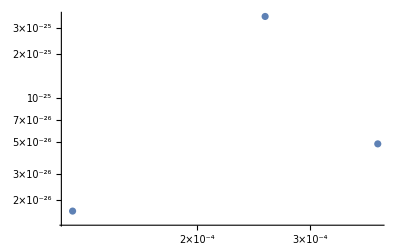

```mathematica
ListLogLogPlot[plhhVfreq]
```

```mathematica
{cone, ctwo, cthree}=ColorData[97,"ColorList"][[1;;3]]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885]}

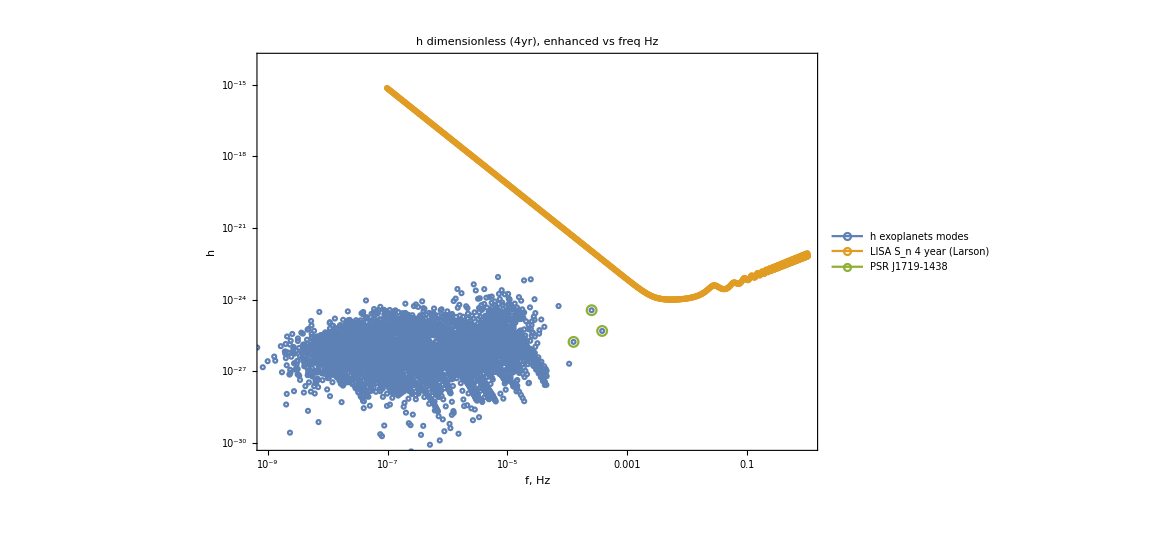

```mathematica
plotNNyearWPl = ListLogLogPlot[{hhVfreq,dataOnlyNNyr, plhhVfreq},
PlotRange->{{10^-9, 10^0},{10^-30,10^-14}},
Joined->{False, True, False},
PlotMarkers->{Graphics[{cone, Circle[]}, ImageSize->4],Graphics[{ctwo, Circle[]}, ImageSize->4],Graphics[{cthree, Thick, Circle[]},ImageSize->10]},
PlotLabel->"h dimensionless ("<>StrAvgYears<>"yr), enhanced vs freq Hz",
AxesLabel->{"f, Hz", "h"},
PlotLegends->Placed[LineLegend[{"h exoplanets modes", "LISA S_n "<>StrAvgYears<>" year (Larson)", "PSR J1719-1438"}, Joined->True],{Right, Top}],
PlotTheme->"Detailed",
ImageSize->{12.0, 8.0}*72.0]
(* !!!!ACK. the axis labels are buggered in this plot!!! *)
```

```mathematica
Export[StrAvgYears2<>"YearLarsonWPl.png", plotNNyearWPl,ImageSize->{12.0, 8.0}*72.0]
```

FourYearLarsonWPl.png

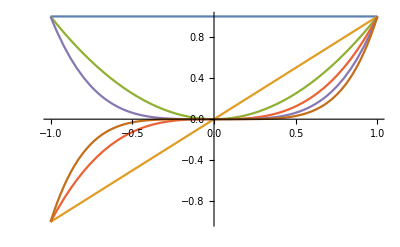

-Graphics-

```mathematica
fns=Table[x^n,{n,0,5}];
Plot[fns,{x,-1,1},PlotStyle->ColorData[97,"ColorList"]]
Plot[fns,{x,-1,1}]
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
aNmax[0.06]
```

3

```mathematica
aNmin[0.06]
```

1

```mathematica
??aNmax
```

The maximum useful mode number, 0.05 of the peak of the g(n,e) curve, given an eccentricity.  Care when used for eccentricities above 0.85.

aNmax[ecc_]:=If[ecc==0,2,Max[{3,Floor[fitEcc2N2[ecc]+1]}]]